```mathematica
SetDirectory["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo"]
Needs["ErrorBarPlots`"]
Get["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/ErrorBarLogPlots.m"]
Get["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/ProtonFluxAnn.m"]
```

/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo

InterpolatingFunction[…]

## AMS02-Experiment Error Bar Import

57

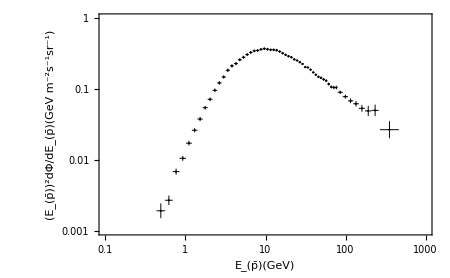

```mathematica
IError = Import[  "/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/Error_data_AMS02_Full.dat","Table",HeaderLines-> 1];
Length[IError]
IError1=Table[{IError[[i,1]],IError[[i,2]],(IError[[i,4]]-IError[[i,3]])/2,(IError[[i,6]]-IError[[i,5]])/2},{i,1,Length[IError]}];
IError2=IError1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPlot1=ErrorListLogLogPlot[IError2,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

393

InterpolatingFunction[…]

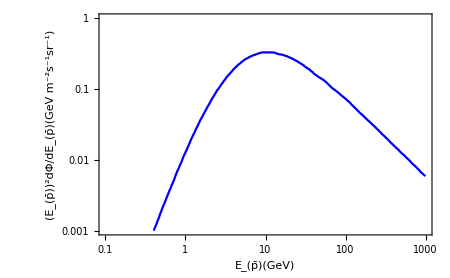

```mathematica
BG00=Import["/Users/sinbi/desktop/AMS02.csv","CSV","HearderLines"->1];
BG01=Table[BG00[[i,All]],{i,7,399}];
Length[BG01]
ifBG0=Interpolation[BG01]
BGPlot=ListLogLogPlot[ifBG0,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Dark Matter(DM)

```mathematica
GeV=1;
topm=173.0GeV;
```

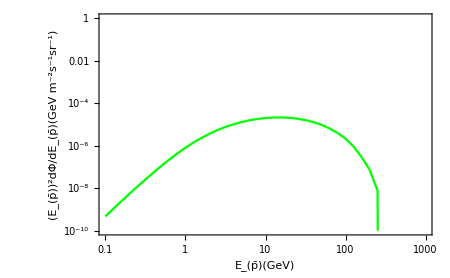

```mathematica
primaryτs="τ";
haloτs="NFW";
propagationτs="MED";
mDMτs=300GeV;
σvτs=10^-26;
Eγτ=10^lEγ;
Poτs=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryτs, haloτs, propagationτs][mDMτs, σvτs,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDτs=ListLogLogPlot[Poτs,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

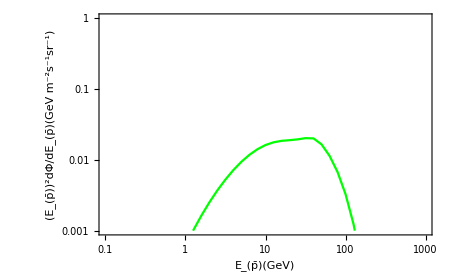

```mathematica
primarybs="b";
halobs="NFW";
propagationbs="MED";
mDMbs=300GeV;
σvbs=3×σvτs;
Eγs=10^lEγ;
Pobs=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarybs, halobs, propagationbs][mDMbs, σvbs,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDbs=ListLogLogPlot[Pobs,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

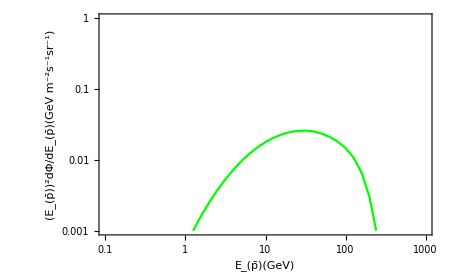

```mathematica
primarycs="c";
halocs="NFW";
propagationcs="MED";
mDMcs=300GeV;
σvcs=3×σvτs;
Eγc=10^lEγ;
Pocs=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarycs, halocs, propagationcs][mDMcs, σvcs,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDcs=ListLogLogPlot[Pocs,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

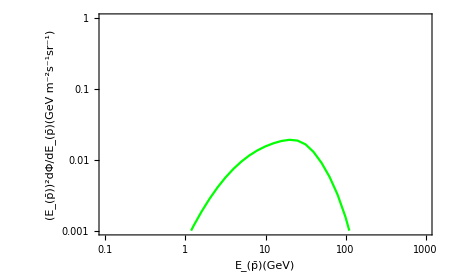

```mathematica
primaryts="t";
halots="NFW";
propagationts="MED";
mDMts=300GeV;
σvts=3×σvτs;
Eγt=10^lEγ;
Pots=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryts, halots, propagationts][mDMts, σvts,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDts=ListLogLogPlot[Pots,Joined->True,PlotRange->{{10^-1,10^3},{10^-3,1}},PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

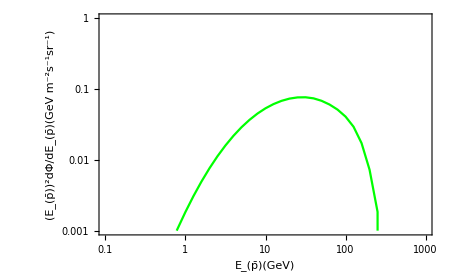

```mathematica
primaryqs="q";
haloqs="NFW";
propagationqs="MED";
mDMqs=300GeV;
σvqs=9×σvτs;
Eγq=10^lEγ;
Poqs=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryqs, haloqs, propagationqs][mDMqs, σvqs,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDqs=ListLogLogPlot[Poqs,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

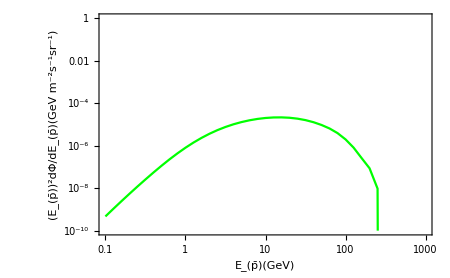

```mathematica
primaryes="e";
haloes="NFW";
propagationes="MED";
mDMes=300GeV;
σves=σvτs;
Eγe=10^lEγ;
Poes=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryes, haloes, propagationes][mDMes, σves,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDes=ListLogLogPlot[Poes,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

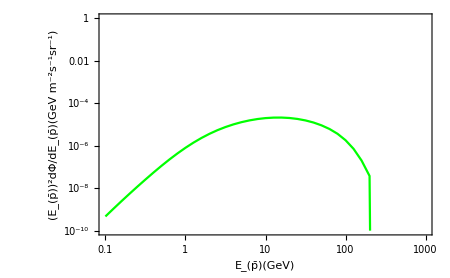

```mathematica
primaryμs="μ";
haloμs="NFW";
propagationμs="MED";
mDMμs=300GeV;
σvμs=σvτs;
Eγμ=10^lEγ;
Poμs=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryμs, haloμs, propagationμs][mDMμs, σvμs,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDμs=ListLogLogPlot[Poμs,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

```mathematica
Length[Poμs]
Length[Poes]
Length[Pots]
Length[Poτs]
Length[Pocs]
Length[Pobs]
Length[Poqs]
```

401

401

401

«4 more identical outputs»

```mathematica
ifPot1=Table[{Poμs[[i,1]],(Poμs[[i,2]]+Poes[[i,2]]+Pots[[i,2]]+Poτs[[i,2]]+Pocs[[i,2]]+Pobs[[i,2]]+Poqs[[i,2]])},{i,1,Length[Poμs]}];
Length[ifPot1]
ifPot1f=Interpolation[ifPot1]
```

401

InterpolatingFunction[…]

```mathematica
ifPot2=Table[{Poμs[[i,1]],(Poμs[[i,2]]+Poes[[i,2]]+Poτs[[i,2]]+Pocs[[i,2]]+Pobs[[i,2]]+Poqs[[i,2]])},{i,1,Length[Poμs]}];
Length[ifPot2]
ifPot2f=Interpolation[ifPot2]
```

401

InterpolatingFunction[…]

```mathematica
Sumdemo01=Table[{x,ifBG0[x]+ifPot1f[x]},{x,0.18,10^2.99,0.1}]
Sumdemo02=Table[{x,ifBG0[x]+ifPot2f[x]},{x,0.18,10^2.99,0.1}]
```

{{0.18,0.000138226},{0.28,0.000458032},{0.38,0.00113499},{0.48,0.00224871},9763,{976.88,0.00597304},{976.98,0.00597254},{977.08,0.00597203},{977.18,0.00597153}}
 |  |  |  |

{{0.18,0.00013319},{0.28,0.000437317},{0.38,0.00108248},{0.48,0.00214478},9763,{976.88,0.00597304},{976.98,0.00597254},{977.08,0.00597203},{977.18,0.00597153}}
 |  |  |  |

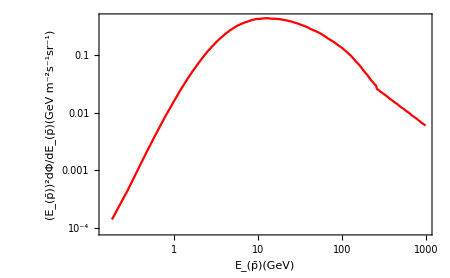

```mathematica
SumPlotifPot1=ListLogLogPlot[Sumdemo01,Joined->True,PlotStyle->Red,Frame->True,Axes->False,ImageSize->450 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

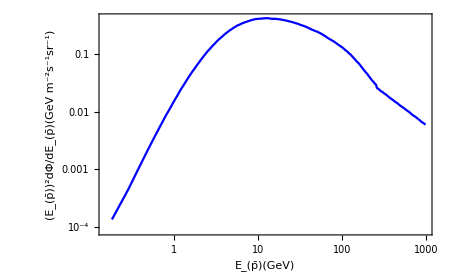

```mathematica
SumPlotifPot2=ListLogLogPlot[Sumdemo02,Joined->True,PlotStyle->Blue,Frame->True,Axes->False,ImageSize->450 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

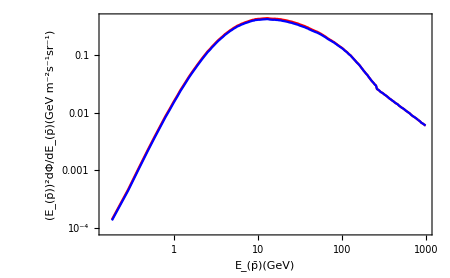

```mathematica
Show[SumPlotifPot1,SumPlotifPot2]
```

## χ^2- Fitting

```mathematica
SumY1=Table[Sumdemo01[IError1[[i,1]]],{i,Length[IError]}];
IErrorY1=Flatten[Table[{IError1[[i,2]]},{i,1,Length[IError]}],1];
IErrorSize1=Flatten[Table[{IError1[[i,4]]},{i,1,Length[IError]}],1];
chiSUM1=((SumY1-IErrorY1)/IErrorSize1)^2;
Sum[chiSUM1[[i]],{i,1,Length[IError]}];
```

```mathematica
SumY2=Table[Sumdemo02[IError1[[i,1]]],{i,Length[IError]}];
IErrorY2=Flatten[Table[{IError1[[i,2]]},{i,1,Length[IError]}],1];
IErrorSize2=Flatten[Table[{IError1[[i,4]]},{i,1,Length[IError]}],1];
chiSUM2=((SumY2-IErrorY2)/IErrorSize2)^2;
Sum[chiSUM2[[i]],{i,1,Length[IError]}];
```

## Mass-σv graph

```mathematica
ClearAll[σv2,mDM2]
```

```mathematica
σv2=10^lσv2;
mDM2=10^lmDM2;
```

```mathematica
Poτs2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryτs, haloτs, propagationτs][mDM2, σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Pobs2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarybs, halobs, propagationbs][mDM2, 3*σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Pocs2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarycs, halocs, propagationcs][mDM2, 3*σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Pots2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryts, halots, propagationts][mDM2, 3*σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poes2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryes, haloes, propagationes][mDM2, σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poμs2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryμs, haloμs,propagationμs][mDM2, σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poqs2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryqs, haloqs, propagationqs][mDM2, 3*3*σv2,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
```

```mathematica
ifPot3=Table[{Poμs[[i,1]],(Poμs2[[i,2]]+Poes2[[i,2]]+Pots2[[i,2]]+Poτs2[[i,2]]+Pocs2[[i,2]]+Pobs2[[i,2]]+Poqs2[[i,2]])},{i,1,Length[Poμs2]}]
ifPot3f=Interpolation[ifPot3];
ifPot4=Table[{Poμs2[[i,1]],(Poμs2[[i,2]]+Poes2[[i,2]]+Poτs2[[i,2]]+Pocs2[[i,2]]+Pobs2[[i,2]]+Poqs2[[i,2]])},{i,1,Length[Poμs2]}]
ifPot4f=Interpolation[ifPot4];
```

{{0.1,0.1 10.^If[0.1>10^lmDM2||10^lmDM2<0,-∞,Log10[(9 10^lσv2)/σvref]+tabΦpbarAnnI[q,NFW,MED][1]]+0.1 10.^If[1]+0.1 10.^1+0.1 1+0.1 1+0.1 10.^If[1]+0.1 10.^If[0.1>10^lmDM2||1,-∞,1]},400}
 |  |  |  |

{{0.1,0.1 10.^If[0.1>10^lmDM2||10^lmDM2<0,-∞,Log10[(9 10^lσv2)/σvref]+tabΦpbarAnnI[q,NFW,MED][1]]+0.1 10.^If[1]+0.1 10.^1+0.1 1+0.1 10.^If[1]+0.1 10.^If[0.1>10^lmDM2||1,-∞,1]},399,{1000.,1}}
 |  |  |  |

```mathematica
Sumdemo03=Interpolation[Table[{x,ifBG0[x]+ifPot3f[x]},{x,0.18,10^2.99,0.1}]];
Sumdemo04=Interpolation[Table[{x,ifBG0[x]+ifPot4f[x]},{x,0.18,10^2.99,0.1}]];
```

```mathematica
SumY3=Table[Sumdemo03[IError1[[i,1]]],{i,Length[IError]}];
chiSUMY03=((SumY3-IErrorY1)/IErrorSize1)^2;
FinalSum03d=Sum[chiSUMY03[[i]],{i,1,Length[IError]}];
SumY4=Table[Sumdemo04[IError1[[i,1]]],{i,Length[IError]}];
chiSUMY04=((SumY4-IErrorY1)/IErrorSize1)^2;
FinalSum04d=Sum[chiSUMY04[[i]],{i,1,Length[IError]}];
```

```mathematica
Log10[10^-28/21.]
```

-29.3222

```mathematica
contdemo1=Flatten[Table[{mDM2,Log[10, 18*σv2],18*σv2,FinalSum04d},{lmDM2,0.7,Log10[topm],0.02},{lσv2,-29.26,-26.26,0.05}],1]
Export["contour_AMS_RED_Demo01.dat",contdemo1,"Table"];
(*contdemo1=Flatten[Table[{mDM2,Log[10, 21*σv2],21*σv2,If[mDM2>Log10[173.21],FinalSum03]},{lmDM2,0.7,2.4,0.05},{lσv2,-29.32,-26.32,0.05}],1]
Export["contour_AMS_Demo01.dat",contdemo1,"Table"];*)
contdemo2=Flatten[Table[{mDM2,Log[10, 21*σv2],21*σv2,FinalSum03d},{lmDM2,Log10[topm],2.4,0.02},{lσv2,-29.32,-26.32,0.05}],1]
Export["contour_AMS_RED_Demo02.dat",contdemo2,"Table"];
contdemo3=Join[contdemo1,contdemo2]
Export["contour_AMS_RED_Demo03.dat",contdemo3,"Table"]
```

{{5.01187,-28.0047,9.89174×10^-29,154.509},{5.01187,-27.9547,1.10987×10^-28,156.27},4694,{165.959,-25.0047,9.89174×10^-26,5332.42}}
 |  |  |  |

{{173.,-27.9978,1.00512×10^-28,151.586},{173.,-27.9478,1.12777×10^-28,151.481},{173.,-27.8978,1.26538×10^-28,151.364},{173.,-27.8478,1.41977×10^-28,151.233},{173.,-27.7978,1.59301×10^-28,151.086},{173.,-27.7478,1.78739×10^-28,150.921},{173.,-27.6978,2.00548×10^-28,150.737},{173.,-27.6478,2.25019×10^-28,150.531},{173.,-27.5978,2.52476×10^-28,150.3},{173.,-27.5478,2.83282×10^-28,150.042},{173.,-27.4978,3.17848×10^-28,149.753},{173.,-27.4478,3.56631×10^-28,149.43},{173.,-27.3978,4.00147×10^-28,149.07},{173.,-27.3478,4.48972×10^-28,148.667},{173.,-27.2978,5.03755×10^-28,148.218},{173.,-27.2478,5.65222×10^-28,147.717},{173.,-27.1978,6.3419×10^-28,147.158},{173.,-27.1478,7.11573×10^-28,146.537},{173.,-27.0978,7.98398×10^-28,145.846},{173.,-27.0478,8.95817×10^-28,145.078},{173.,-26.9978,1.00512×10^-27,144.227},{173.,-26.9478,1.12777×10^-27,143.284},{173.,-26.8978,1.26538×10^-27,142.241},{173.,-26.8478,1.41977×10^-27,141.091},{173.,-26.7978,1.59301×10^-27,139.826},{173.,-26.7478,1.78739×10^-27,138.436},{173.,-26.6978,2.00548×10^-27,136.917},{173.,-26.6478,2.25019×10^-27,135.261},{173.,-26.5978,2.52476×10^-27,133.466},{173.,-26.5478,2.83282×10^-27,131.529},{173.,-26.4978,3.17848×10^-27,129.454},{173.,-26.4478,3.56631×10^-27,127.249},{173.,-26.3978,4.00147×10^-27,124.931},{173.,-26.3478,4.48972×10^-27,122.526},{173.,-26.2978,5.03755×10^-27,120.075},{173.,-26.2478,5.65222×10^-27,117.634},{173.,-26.1978,6.3419×10^-27,115.287},{173.,-26.1478,7.11573×10^-27,113.146},{173.,-26.0978,7.98398×10^-27,111.363},{173.,-26.0478,8.95817×10^-27,110.143},{173.,-25.9978,1.00512×10^-26,109.756},{173.,-25.9478,1.12777×10^-26,110.557},{173.,-25.8978,1.26538×10^-26,113.013},{173.,-25.8478,1.41977×10^-26,117.728},{173.,-25.7978,1.59301×10^-26,125.485},{173.,-25.7478,1.78739×10^-26,137.294},{173.,-25.6978,2.00548×10^-26,154.453},{173.,-25.6478,2.25019×10^-26,178.628},{173.,-25.5978,2.52476×10^-26,211.948},{173.,-25.5478,2.83282×10^-26,257.135},{173.,-25.4978,3.17848×10^-26,317.655},{173.,-25.4478,3.56631×10^-26,397.922},{173.,-25.3978,4.00147×10^-26,503.547},{173.,-25.3478,4.48972×10^-26,641.654},{173.,-25.2978,5.03755×10^-26,821.28},{173.,-25.2478,5.65222×10^-26,1053.88},{173.,-25.1978,6.3419×10^-26,1353.95},{173.,-25.1478,7.11573×10^-26,1739.85},{173.,-25.0978,7.98398×10^-26,2234.8},{173.,-25.0478,8.95817×10^-26,2868.15},{173.,-24.9978,1.00512×10^-25,3676.98},{181.153,-27.9978,1.00512×10^-28,151.517},{181.153,-27.9478,1.12777×10^-28,151.404},{181.153,-27.8978,1.26538×10^-28,151.278},{181.153,-27.8478,1.41977×10^-28,151.136},{181.153,-27.7978,1.59301×10^-28,150.978},{181.153,-27.7478,1.78739×10^-28,150.8},{181.153,-27.6978,2.00548×10^-28,150.601},{181.153,-27.6478,2.25019×10^-28,150.378},{181.153,-27.5978,2.52476×10^-28,150.129},{181.153,-27.5478,2.83282×10^-28,149.85},{181.153,-27.4978,3.17848×10^-28,149.538},{181.153,-27.4478,3.56631×10^-28,149.19},{181.153,-27.3978,4.00147×10^-28,148.8},{181.153,-27.3478,4.48972×10^-28,148.365},{181.153,-27.2978,5.03755×10^-28,147.88},{181.153,-27.2478,5.65222×10^-28,147.339},{181.153,-27.1978,6.3419×10^-28,146.736},{181.153,-27.1478,7.11573×10^-28,146.064},{181.153,-27.0978,7.98398×10^-28,145.318},{181.153,-27.0478,8.95817×10^-28,144.488},{181.153,-26.9978,1.00512×10^-27,143.568},{181.153,-26.9478,1.12777×10^-27,142.549},{181.153,-26.8978,1.26538×10^-27,141.422},{181.153,-26.8478,1.41977×10^-27,140.178},{181.153,-26.7978,1.59301×10^-27,138.809},{181.153,-26.7478,1.78739×10^-27,137.306},{181.153,-26.6978,2.00548×10^-27,135.661},{181.153,-26.6478,2.25019×10^-27,133.868},{181.153,-26.5978,2.52476×10^-27,131.922},{181.153,-26.5478,2.83282×10^-27,129.822},{181.153,-26.4978,3.17848×10^-27,127.571},{181.153,-26.4478,3.56631×10^-27,125.177},{181.153,-26.3978,4.00147×10^-27,122.657},{181.153,-26.3478,4.48972×10^-27,120.038},{181.153,-26.2978,5.03755×10^-27,117.363},{181.153,-26.2478,5.65222×10^-27,114.692},{181.153,-26.1978,6.3419×10^-27,112.113},{181.153,-26.1478,7.11573×10^-27,109.745},{181.153,-26.0978,7.98398×10^-27,107.748},{181.153,-26.0478,8.95817×10^-27,106.34},{181.153,-25.9978,1.00512×10^-26,105.807},{181.153,-25.9478,1.12777×10^-26,106.528},{181.153,-25.8978,1.26538×10^-26,108.998},{181.153,-25.8478,1.41977×10^-26,113.859},{181.153,-25.7978,1.59301×10^-26,121.945},{181.153,-25.7478,1.78739×10^-26,134.33},{181.153,-25.6978,2.00548×10^-26,152.396},{181.153,-25.6478,2.25019×10^-26,177.918},{181.153,-25.5978,2.52476×10^-26,213.163},{181.153,-25.5478,2.83282×10^-26,261.031},{181.153,-25.4978,3.17848×10^-26,325.214},{181.153,-25.4478,3.56631×10^-26,410.418},{181.153,-25.3978,4.00147×10^-26,522.621},{181.153,-25.3478,4.48972×10^-26,669.416},{181.153,-25.2978,5.03755×10^-26,860.438},{181.153,-25.2478,5.65222×10^-26,1107.89},{181.153,-25.1978,6.3419×10^-26,1427.25},{181.153,-25.1478,7.11573×10^-26,1838.08},{181.153,-25.0978,7.98398×10^-26,2365.13},{181.153,-25.0478,8.95817×10^-26,3039.71},{181.153,-24.9978,1.00512×10^-25,3901.35},{189.691,-27.9978,1.00512×10^-28,151.566},{189.691,-27.9478,1.12777×10^-28,151.459},{189.691,-27.8978,1.26538×10^-28,151.339},{189.691,-27.8478,1.41977×10^-28,151.205},{189.691,-27.7978,1.59301×10^-28,151.054},{189.691,-27.7478,1.78739×10^-28,150.886},{189.691,-27.6978,2.00548×10^-28,150.697},{189.691,-27.6478,2.25019×10^-28,150.486},{189.691,-27.5978,2.52476×10^-28,150.25},{189.691,-27.5478,2.83282×10^-28,149.985},{189.691,-27.4978,3.17848×10^-28,149.689},{189.691,-27.4478,3.56631×10^-28,149.359},{189.691,-27.3978,4.00147×10^-28,148.989},{189.691,-27.3478,4.48972×10^-28,148.577},{189.691,-27.2978,5.03755×10^-28,148.116},{189.691,-27.2478,5.65222×10^-28,147.603},{189.691,-27.1978,6.3419×10^-28,147.03},{189.691,-27.1478,7.11573×10^-28,146.393},{189.691,-27.0978,7.98398×10^-28,145.684},{189.691,-27.0478,8.95817×10^-28,144.896},{189.691,-26.9978,1.00512×10^-27,144.022},{189.691,-26.9478,1.12777×10^-27,143.053},{189.691,-26.8978,1.26538×10^-27,141.981},{189.691,-26.8478,1.41977×10^-27,140.798},{189.691,-26.7978,1.59301×10^-27,139.494},{189.691,-26.7478,1.78739×10^-27,138.063},{189.691,-26.6978,2.00548×10^-27,136.495},{189.691,-26.6478,2.25019×10^-27,134.784},{189.691,-26.5978,2.52476×10^-27,132.926},{189.691,-26.5478,2.83282×10^-27,130.918},{189.691,-26.4978,3.17848×10^-27,128.761},{189.691,-26.4478,3.56631×10^-27,126.463},{189.691,-26.3978,4.00147×10^-27,124.039},{189.691,-26.3478,4.48972×10^-27,121.511},{189.691,-26.2978,5.03755×10^-27,118.919},{189.691,-26.2478,5.65222×10^-27,116.315},{189.691,-26.1978,6.3419×10^-27,113.78},{189.691,-26.1478,7.11573×10^-27,111.42},{189.691,-26.0978,7.98398×10^-27,109.383},{189.691,-26.0478,8.95817×10^-27,107.867},{189.691,-25.9978,1.00512×10^-26,107.133},{189.691,-25.9478,1.12777×10^-26,107.527},{189.691,-25.8978,1.26538×10^-26,109.504},{189.691,-25.8478,1.41977×10^-26,113.654},{189.691,-25.7978,1.59301×10^-26,120.74},{189.691,-25.7478,1.78739×10^-26,131.752},{189.691,-25.6978,2.00548×10^-26,147.96},{189.691,-25.6478,2.25019×10^-26,170.997},{189.691,-25.5978,2.52476×10^-26,202.952},{189.691,-25.5478,2.83282×10^-26,246.493},{189.691,-25.4978,3.17848×10^-26,305.025},{189.691,-25.4478,3.56631×10^-26,382.883},{189.691,-25.3978,4.00147×10^-26,485.58},{189.691,-25.3478,4.48972×10^-26,620.119},{189.691,-25.2978,5.03755×10^-26,795.385},{189.691,-25.2478,5.65222×10^-26,1022.64},{189.691,-25.1978,6.3419×10^-26,1316.16},{189.691,-25.1478,7.11573×10^-26,1694.},{189.691,-25.0978,7.98398×10^-26,2179.},{189.691,-25.0478,8.95817×10^-26,2800.06},{189.691,-24.9978,1.00512×10^-25,3593.69},{198.631,-27.9978,1.00512×10^-28,151.612},{198.631,-27.9478,1.12777×10^-28,151.511},{198.631,-27.8978,1.26538×10^-28,151.397},{198.631,-27.8478,1.41977×10^-28,151.27},{198.631,-27.7978,1.59301×10^-28,151.127},{198.631,-27.7478,1.78739×10^-28,150.968},{198.631,-27.6978,2.00548×10^-28,150.789},{198.631,-27.6478,2.25019×10^-28,150.589},{198.631,-27.5978,2.52476×10^-28,150.364},{198.631,-27.5478,2.83282×10^-28,150.114},{198.631,-27.4978,3.17848×10^-28,149.833},{198.631,-27.4478,3.56631×10^-28,149.52},{198.631,-27.3978,4.00147×10^-28,149.17},{198.631,-27.3478,4.48972×10^-28,148.778},{198.631,-27.2978,5.03755×10^-28,148.342},{198.631,-27.2478,5.65222×10^-28,147.854},{198.631,-27.1978,6.3419×10^-28,147.311},{198.631,-27.1478,7.11573×10^-28,146.706},{198.631,-27.0978,7.98398×10^-28,146.033},{198.631,-27.0478,8.95817×10^-28,145.285},{198.631,-26.9978,1.00512×10^-27,144.455},{198.631,-26.9478,1.12777×10^-27,143.534},{198.631,-26.8978,1.26538×10^-27,142.516},{198.631,-26.8478,1.41977×10^-27,141.391},{198.631,-26.7978,1.59301×10^-27,140.151},{198.631,-26.7478,1.78739×10^-27,138.788},{198.631,-26.6978,2.00548×10^-27,137.295},{198.631,-26.6478,2.25019×10^-27,135.664},{198.631,-26.5978,2.52476×10^-27,133.891},{198.631,-26.5478,2.83282×10^-27,131.972},{198.631,-26.4978,3.17848×10^-27,129.909},{198.631,-26.4478,3.56631×10^-27,127.706},{198.631,-26.3978,4.00147×10^-27,125.377},{198.631,-26.3478,4.48972×10^-27,122.942},{198.631,-26.2978,5.03755×10^-27,120.435},{198.631,-26.2478,5.65222×10^-27,117.905},{198.631,-26.1978,6.3419×10^-27,115.423},{198.631,-26.1478,7.11573×10^-27,113.086},{198.631,-26.0978,7.98398×10^-27,111.029},{198.631,-26.0478,8.95817×10^-27,109.432},{198.631,-25.9978,1.00512×10^-26,108.535},{198.631,-25.9478,1.12777×10^-26,108.655},{198.631,-25.8978,1.26538×10^-26,110.208},{198.631,-25.8478,1.41977×10^-26,113.736},{198.631,-25.7978,1.59301×10^-26,119.943},{198.631,-25.7478,1.78739×10^-26,129.738},{198.631,-25.6978,2.00548×10^-26,144.29},{198.631,-25.6478,2.25019×10^-26,165.104},{198.631,-25.5978,2.52476×10^-26,194.105},{198.631,-25.5478,2.83282×10^-26,233.753},{198.631,-25.4978,3.17848×10^-26,287.189},{198.631,-25.4478,3.56631×10^-26,358.412},{198.631,-25.3978,4.00147×10^-26,452.511},{198.631,-25.3478,4.48972×10^-26,575.948},{198.631,-25.2978,5.03755×10^-26,736.928},{198.631,-25.2478,5.65222×10^-26,945.852},{198.631,-25.1978,6.3419×10^-26,1215.9},{198.631,-25.1478,7.11573×10^-26,1563.75},{198.631,-25.0978,7.98398×10^-26,2010.52},{198.631,-25.0478,8.95817×10^-26,2582.89},{198.631,-24.9978,1.00512×10^-25,3314.6},{207.992,-27.9978,1.00512×10^-28,151.654},{207.992,-27.9478,1.12777×10^-28,151.557},{207.992,-27.8978,1.26538×10^-28,151.449},{207.992,-27.8478,1.41977×10^-28,151.328},{207.992,-27.7978,1.59301×10^-28,151.193},{207.992,-27.7478,1.78739×10^-28,151.041},{207.992,-27.6978,2.00548×10^-28,150.871},{207.992,-27.6478,2.25019×10^-28,150.681},{207.992,-27.5978,2.52476×10^-28,150.468},{207.992,-27.5478,2.83282×10^-28,150.229},{207.992,-27.4978,3.17848×10^-28,149.963},{207.992,-27.4478,3.56631×10^-28,149.665},{207.992,-27.3978,4.00147×10^-28,149.331},{207.992,-27.3478,4.48972×10^-28,148.959},{207.992,-27.2978,5.03755×10^-28,148.544},{207.992,-27.2478,5.65222×10^-28,148.08},{207.992,-27.1978,6.3419×10^-28,147.563},{207.992,-27.1478,7.11573×10^-28,146.987},{207.992,-27.0978,7.98398×10^-28,146.346},{207.992,-27.0478,8.95817×10^-28,145.634},{207.992,-26.9978,1.00512×10^-27,144.843},{207.992,-26.9478,1.12777×10^-27,143.965},{207.992,-26.8978,1.26538×10^-27,142.994},{207.992,-26.8478,1.41977×10^-27,141.92},{207.992,-26.7978,1.59301×10^-27,140.737},{207.992,-26.7478,1.78739×10^-27,139.435},{207.992,-26.6978,2.00548×10^-27,138.006},{207.992,-26.6478,2.25019×10^-27,136.445},{207.992,-26.5978,2.52476×10^-27,134.746},{207.992,-26.5478,2.83282×10^-27,132.905},{207.992,-26.4978,3.17848×10^-27,130.921},{207.992,-26.4478,3.56631×10^-27,128.8},{207.992,-26.3978,4.00147×10^-27,126.55},{207.992,-26.3478,4.48972×10^-27,124.191},{207.992,-26.2978,5.03755×10^-27,121.751},{207.992,-26.2478,5.65222×10^-27,119.274},{207.992,-26.1978,6.3419×10^-27,116.823},{207.992,-26.1478,7.11573×10^-27,114.487},{207.992,-26.0978,7.98398×10^-27,112.387},{207.992,-26.0478,8.95817×10^-27,110.685},{207.992,-25.9978,1.00512×10^-26,109.601},{207.992,-25.9478,1.12777×10^-26,109.424},{207.992,-25.8978,1.26538×10^-26,110.532},{207.992,-25.8478,1.41977×10^-26,113.422},{207.992,-25.7978,1.59301×10^-26,118.737},{207.992,-25.7478,1.78739×10^-26,127.311},{207.992,-25.6978,2.00548×10^-26,140.215},{207.992,-25.6478,2.25019×10^-26,158.829},{207.992,-25.5978,2.52476×10^-26,184.92},{207.992,-25.5478,2.83282×10^-26,220.749},{207.992,-25.4978,3.17848×10^-26,269.2},{207.992,-25.4478,3.56631×10^-26,333.952},{207.992,-25.3978,4.00147×10^-26,419.681},{207.992,-25.3478,4.48972×10^-26,532.334},{207.992,-25.2978,5.03755×10^-26,679.459},{207.992,-25.2478,5.65222×10^-26,870.627},{207.992,-25.1978,6.3419×10^-26,1117.97},{207.992,-25.1478,7.11573×10^-26,1436.85},{207.992,-25.0978,7.98398×10^-26,1846.69},{207.992,-25.0478,8.95817×10^-26,2372.09},{207.992,-24.9978,1.00512×10^-25,3044.1},{217.794,-27.9978,1.00512×10^-28,151.694},{217.794,-27.9478,1.12777×10^-28,151.603},{217.794,-27.8978,1.26538×10^-28,151.501},{217.794,-27.8478,1.41977×10^-28,151.386},{217.794,-27.7978,1.59301×10^-28,151.257},{217.794,-27.7478,1.78739×10^-28,151.113},{217.794,-27.6978,2.00548×10^-28,150.952},{217.794,-27.6478,2.25019×10^-28,150.771},{217.794,-27.5978,2.52476×10^-28,150.569},{217.794,-27.5478,2.83282×10^-28,150.343},{217.794,-27.4978,3.17848×10^-28,150.09},{217.794,-27.4478,3.56631×10^-28,149.807},{217.794,-27.3978,4.00147×10^-28,149.49},{217.794,-27.3478,4.48972×10^-28,149.137},{217.794,-27.2978,5.03755×10^-28,148.742},{217.794,-27.2478,5.65222×10^-28,148.302},{217.794,-27.1978,6.3419×10^-28,147.811},{217.794,-27.1478,7.11573×10^-28,147.263},{217.794,-27.0978,7.98398×10^-28,146.654},{217.794,-27.0478,8.95817×10^-28,145.977},{217.794,-26.9978,1.00512×10^-27,145.224},{217.794,-26.9478,1.12777×10^-27,144.389},{217.794,-26.8978,1.26538×10^-27,143.464},{217.794,-26.8478,1.41977×10^-27,142.442},{217.794,-26.7978,1.59301×10^-27,141.314},{217.794,-26.7478,1.78739×10^-27,140.072},{217.794,-26.6978,2.00548×10^-27,138.709},{217.794,-26.6478,2.25019×10^-27,137.218},{217.794,-26.5978,2.52476×10^-27,135.593},{217.794,-26.5478,2.83282×10^-27,133.83},{217.794,-26.4978,3.17848×10^-27,131.928},{217.794,-26.4478,3.56631×10^-27,129.889},{217.794,-26.3978,4.00147×10^-27,127.722},{217.794,-26.3478,4.48972×10^-27,125.442},{217.794,-26.2978,5.03755×10^-27,123.075},{217.794,-26.2478,5.65222×10^-27,120.66},{217.794,-26.1978,6.3419×10^-27,118.252},{217.794,-26.1478,7.11573×10^-27,115.931},{217.794,-26.0978,7.98398×10^-27,113.806},{217.794,-26.0478,8.95817×10^-27,112.026},{217.794,-25.9978,1.00512×10^-26,110.789},{217.794,-25.9478,1.12777×10^-26,110.357},{217.794,-25.8978,1.26538×10^-26,111.077},{217.794,-25.8478,1.41977×10^-26,113.4},{217.794,-25.7978,1.59301×10^-26,117.916},{217.794,-25.7478,1.78739×10^-26,125.386},{217.794,-25.6978,2.00548×10^-26,136.793},{217.794,-25.6478,2.25019×10^-26,153.4},{217.794,-25.5978,2.52476×10^-26,176.827},{217.794,-25.5478,2.83282×10^-26,209.149},{217.794,-25.4978,3.17848×10^-26,253.014},{217.794,-25.4478,3.56631×10^-26,311.798},{217.794,-25.3978,4.00147×10^-26,389.797},{217.794,-25.3478,4.48972×10^-26,492.475},{217.794,-25.2978,5.03755×10^-26,626.77},{217.794,-25.2478,5.65222×10^-26,801.48},{217.794,-25.1978,6.3419×10^-26,1027.76},{217.794,-25.1478,7.11573×10^-26,1319.73},{217.794,-25.0978,7.98398×10^-26,1695.28},{217.794,-25.0478,8.95817×10^-26,2177.01},{217.794,-24.9978,1.00512×10^-25,2793.5},{228.058,-27.9978,1.00512×10^-28,151.733},{228.058,-27.9478,1.12777×10^-28,151.646},{228.058,-27.8978,1.26538×10^-28,151.549},{228.058,-27.8478,1.41977×10^-28,151.44},{228.058,-27.7978,1.59301×10^-28,151.318},{228.058,-27.7478,1.78739×10^-28,151.181},{228.058,-27.6978,2.00548×10^-28,151.028},{228.058,-27.6478,2.25019×10^-28,150.856},{228.058,-27.5978,2.52476×10^-28,150.664},{228.058,-27.5478,2.83282×10^-28,150.45},{228.058,-27.4978,3.17848×10^-28,150.209},{228.058,-27.4478,3.56631×10^-28,149.94},{228.058,-27.3978,4.00147×10^-28,149.64},{228.058,-27.3478,4.48972×10^-28,149.304},{228.058,-27.2978,5.03755×10^-28,148.929},{228.058,-27.2478,5.65222×10^-28,148.51},{228.058,-27.1978,6.3419×10^-28,148.044},{228.058,-27.1478,7.11573×10^-28,147.523},{228.058,-27.0978,7.98398×10^-28,146.944},{228.058,-27.0478,8.95817×10^-28,146.299},{228.058,-26.9978,1.00512×10^-27,145.583},{228.058,-26.9478,1.12777×10^-27,144.788},{228.058,-26.8978,1.26538×10^-27,143.907},{228.058,-26.8478,1.41977×10^-27,142.933},{228.058,-26.7978,1.59301×10^-27,141.858},{228.058,-26.7478,1.78739×10^-27,140.673},{228.058,-26.6978,2.00548×10^-27,139.371},{228.058,-26.6478,2.25019×10^-27,137.946},{228.058,-26.5978,2.52476×10^-27,136.391},{228.058,-26.5478,2.83282×10^-27,134.701},{228.058,-26.4978,3.17848×10^-27,132.875},{228.058,-26.4478,3.56631×10^-27,130.914},{228.058,-26.3978,4.00147×10^-27,128.825},{228.058,-26.3478,4.48972×10^-27,126.62},{228.058,-26.2978,5.03755×10^-27,124.321},{228.058,-26.2478,5.65222×10^-27,121.963},{228.058,-26.1978,6.3419×10^-27,119.595},{228.058,-26.1478,7.11573×10^-27,117.288},{228.058,-26.0978,7.98398×10^-27,115.14},{228.058,-26.0478,8.95817×10^-27,113.284},{228.058,-25.9978,1.00512×10^-26,111.901},{228.058,-25.9478,1.12777×10^-26,111.227},{228.058,-25.8978,1.26538×10^-26,111.578},{228.058,-25.8478,1.41977×10^-26,113.366},{228.058,-25.7978,1.59301×10^-26,117.125},{228.058,-25.7478,1.78739×10^-26,123.551},{228.058,-25.6978,2.00548×10^-26,133.54},{228.058,-25.6478,2.25019×10^-26,148.249},{228.058,-25.5978,2.52476×10^-26,169.157},{228.058,-25.5478,2.83282×10^-26,198.164},{228.058,-25.4978,3.17848×10^-26,237.692},{228.058,-25.4478,3.56631×10^-26,290.834},{228.058,-25.3978,4.00147×10^-26,361.526},{228.058,-25.3478,4.48972×10^-26,454.777},{228.058,-25.2978,5.03755×10^-26,576.945},{228.058,-25.2478,5.65222×10^-26,736.1},{228.058,-25.1978,6.3419×10^-26,942.474},{228.058,-25.1478,7.11573×10^-26,1209.02},{228.058,-25.0978,7.98398×10^-26,1552.16},{228.058,-25.0478,8.95817×10^-26,1992.62},{228.058,-24.9978,1.00512×10^-25,2556.65},{238.806,-27.9978,1.00512×10^-28,151.77},{238.806,-27.9478,1.12777×10^-28,151.687},{238.806,-27.8978,1.26538×10^-28,151.595},{238.806,-27.8478,1.41977×10^-28,151.492},{238.806,-27.7978,1.59301×10^-28,151.376},{238.806,-27.7478,1.78739×10^-28,151.246},{238.806,-27.6978,2.00548×10^-28,151.101},{238.806,-27.6478,2.25019×10^-28,150.938},{238.806,-27.5978,2.52476×10^-28,150.756},{238.806,-27.5478,2.83282×10^-28,150.552},{238.806,-27.4978,3.17848×10^-28,150.324},{238.806,-27.4478,3.56631×10^-28,150.069},{238.806,-27.3978,4.00147×10^-28,149.784},{238.806,-27.3478,4.48972×10^-28,149.465},{238.806,-27.2978,5.03755×10^-28,149.109},{238.806,-27.2478,5.65222×10^-28,148.711},{238.806,-27.1978,6.3419×10^-28,148.268},{238.806,-27.1478,7.11573×10^-28,147.773},{238.806,-27.0978,7.98398×10^-28,147.223},{238.806,-27.0478,8.95817×10^-28,146.61},{238.806,-26.9978,1.00512×10^-27,145.929},{238.806,-26.9478,1.12777×10^-27,145.172},{238.806,-26.8978,1.26538×10^-27,144.334},{238.806,-26.8478,1.41977×10^-27,143.406},{238.806,-26.7978,1.59301×10^-27,142.381},{238.806,-26.7478,1.78739×10^-27,141.252},{238.806,-26.6978,2.00548×10^-27,140.01},{238.806,-26.6478,2.25019×10^-27,138.648},{238.806,-26.5978,2.52476×10^-27,137.161},{238.806,-26.5478,2.83282×10^-27,135.543},{238.806,-26.4978,3.17848×10^-27,133.792},{238.806,-26.4478,3.56631×10^-27,131.907},{238.806,-26.3978,4.00147×10^-27,129.895},{238.806,-26.3478,4.48972×10^-27,127.764},{238.806,-26.2978,5.03755×10^-27,125.535},{238.806,-26.2478,5.65222×10^-27,123.236},{238.806,-26.1978,6.3419×10^-27,120.912},{238.806,-26.1478,7.11573×10^-27,118.625},{238.806,-26.0978,7.98398×10^-27,116.463},{238.806,-26.0478,8.95817×10^-27,114.546},{238.806,-25.9978,1.00512×10^-26,113.036},{238.806,-25.9478,1.12777×10^-26,112.148},{238.806,-25.8978,1.26538×10^-26,112.167},{238.806,-25.8478,1.41977×10^-26,113.467},{238.806,-25.7978,1.59301×10^-26,116.534},{238.806,-25.7478,1.78739×10^-26,122.001},{238.806,-25.6978,2.00548×10^-26,130.685},{238.806,-25.6478,2.25019×10^-26,143.64},{238.806,-25.5978,2.52476×10^-26,162.217},{238.806,-25.5478,2.83282×10^-26,188.15},{238.806,-25.4978,3.17848×10^-26,223.652},{238.806,-25.4478,3.56631×10^-26,271.551},{238.806,-25.3978,4.00147×10^-26,335.447},{238.806,-25.3478,4.48972×10^-26,419.921},{238.806,-25.2978,5.03755×10^-26,530.792},{238.806,-25.2478,5.65222×10^-26,675.45},{238.806,-25.1978,6.3419×10^-26,863.261},{238.806,-25.1478,7.11573×10^-26,1106.09},{238.806,-25.0978,7.98398×10^-26,1418.97},{238.806,-25.0478,8.95817×10^-26,1820.91},{238.806,-24.9978,1.00512×10^-25,2335.96},{250.061,-27.9978,1.00512×10^-28,151.804},{250.061,-27.9478,1.12777×10^-28,151.726},{250.061,-27.8978,1.26538×10^-28,151.638},{250.061,-27.8478,1.41977×10^-28,151.54},{250.061,-27.7978,1.59301×10^-28,151.43},{250.061,-27.7478,1.78739×10^-28,151.307},{250.061,-27.6978,2.00548×10^-28,151.169},{250.061,-27.6478,2.25019×10^-28,151.015},{250.061,-27.5978,2.52476×10^-28,150.842},{250.061,-27.5478,2.83282×10^-28,150.648},{250.061,-27.4978,3.17848×10^-28,150.431},{250.061,-27.4478,3.56631×10^-28,150.189},{250.061,-27.3978,4.00147×10^-28,149.918},{250.061,-27.3478,4.48972×10^-28,149.615},{250.061,-27.2978,5.03755×10^-28,149.276},{250.061,-27.2478,5.65222×10^-28,148.898},{250.061,-27.1978,6.3419×10^-28,148.477},{250.061,-27.1478,7.11573×10^-28,148.007},{250.061,-27.0978,7.98398×10^-28,147.483},{250.061,-27.0478,8.95817×10^-28,146.9},{250.061,-26.9978,1.00512×10^-27,146.251},{250.061,-26.9478,1.12777×10^-27,145.531},{250.061,-26.8978,1.26538×10^-27,144.732},{250.061,-26.8478,1.41977×10^-27,143.848},{250.061,-26.7978,1.59301×10^-27,142.87},{250.061,-26.7478,1.78739×10^-27,141.792},{250.061,-26.6978,2.00548×10^-27,140.606},{250.061,-26.6478,2.25019×10^-27,139.304},{250.061,-26.5978,2.52476×10^-27,137.88},{250.061,-26.5478,2.83282×10^-27,136.329},{250.061,-26.4978,3.17848×10^-27,134.648},{250.061,-26.4478,3.56631×10^-27,132.836},{250.061,-26.3978,4.00147×10^-27,130.895},{250.061,-26.3478,4.48972×10^-27,128.835},{250.061,-26.2978,5.03755×10^-27,126.671},{250.061,-26.2478,5.65222×10^-27,124.428},{250.061,-26.1978,6.3419×10^-27,122.146},{250.061,-26.1478,7.11573×10^-27,119.879},{250.061,-26.0978,7.98398×10^-27,117.707},{250.061,-26.0478,8.95817×10^-27,115.735},{250.061,-25.9978,1.00512×10^-26,114.11},{250.061,-25.9478,1.12777×10^-26,113.026},{250.061,-25.8978,1.26538×10^-26,112.74},{250.061,-25.8478,1.41977×10^-26,113.59},{250.061,-25.7978,1.59301×10^-26,116.019},{250.061,-25.7478,1.78739×10^-26,120.602},{250.061,-25.6978,2.00548×10^-26,128.08},{250.061,-25.6478,2.25019×10^-26,139.414},{250.061,-25.5978,2.52476×10^-26,155.834},{250.061,-25.5478,2.83282×10^-26,178.922},{250.061,-25.4978,3.17848×10^-26,210.698},{250.061,-25.4478,3.56631×10^-26,253.743},{250.061,-25.3978,4.00147×10^-26,311.345},{250.061,-25.3478,4.48972×10^-26,387.69},{250.061,-25.2978,5.03755×10^-26,488.097},{250.061,-25.2478,5.65222×10^-26,619.322},{250.061,-25.1978,6.3419×10^-26,789.933},{250.061,-25.1478,7.11573×10^-26,1010.79},{250.061,-25.0978,7.98398×10^-26,1295.63},{250.061,-25.0478,8.95817×10^-26,1661.87},{250.061,-24.9978,1.00512×10^-25,2131.5}}

{{5.01187,-28.0047,9.89174×10^-29,154.509},{5.01187,-27.9547,1.10987×10^-28,156.27},5243,{250.061,-24.9978,1.00512×10^-25,2131.5}}
 |  |  |  |

contour_AMS_RED_Demo03.dat

```mathematica
contdemo01=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/contour_AMS_RED_Demo01.dat","Table",HeaderLines->1];
contdemo02=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/contour_AMS_RED_Demo02.dat","Table",HeaderLines->1];
contdemo03=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_Demo/contour_AMS_RED_Demo03.dat","Table",HeaderLines->1];
```

```mathematica
contdemoLog01=Table[{contdemo01[[i,1]],contdemo01[[i,2]], contdemo01[[i, 4]]},{i, Length[contdemo01]}];
contdemoLog02=Table[{contdemo02[[i,1]],contdemo02[[i,2]], contdemo02[[i, 4]]},{i, Length[contdemo02]}];
contdemoLog03=Table[{contdemo03[[i,1]],contdemo03[[i,2]], contdemo03[[i, 4]]},{i, Length[contdemo03]}];
```

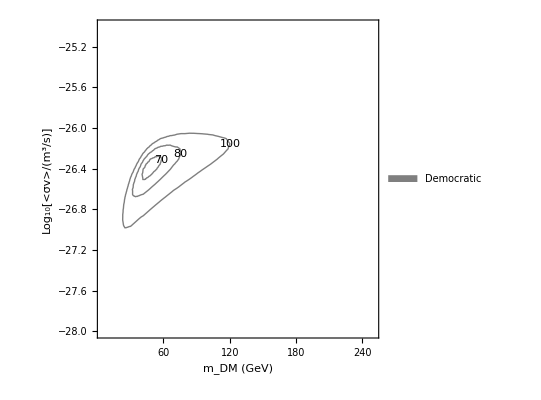

```mathematica
ListContourPlot[contdemoLog03,Contours-> {60, 65,70,80,100},
 FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"}, ContourLabels->All,ContourShading->None,PlotLegends->Placed[SwatchLegend[{"Democratic"},LegendMarkerSize->20],Right]]
```